```mathematica
sample[center_,num_Integer]:=RandomVariate[
MultinormalDistribution[center,{{1,0},{0,1}}],
num];
```

```mathematica
clusters={sample[{-3,-3},10000],sample[{0,0},10000],sample[{3,3},10000]};
```

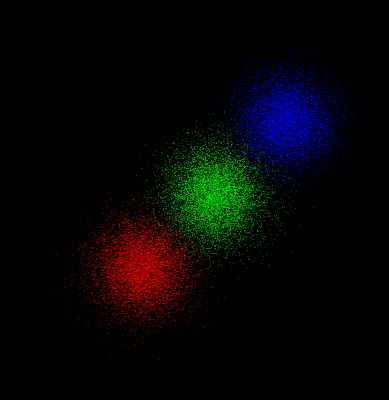

```mathematica
Graphics[{AbsolutePointSize[.1],
MapThread[{#1,Point[#2]}&,{{Red,Green,Blue},clusters}]
},
Background->Black,
PlotRange->10,
Axes->True]
```

```mathematica
net=NetChain[{
DotPlusLayer[400],
ElementwiseLayer[Ramp],
DotPlusLayer[3],
SoftmaxLayer[]
},
"Input"->{2},
"Output"->NetDecoder[{"Class",{Red,Green,Blue}}]
]
```

NetChain[]

```mathematica
NetGraph[net]
```

NetGraph[]

```mathematica
net=NetInitialize[net]
```

NetChain[]

```mathematica
net[{0,0}]
```

RGBColor[0, 0, 1]

```mathematica
data=RandomSample[
Join@@MapThread[
Thread[#1->#2]&,
{clusters,{Red,Green,Blue}}
]];
```

```mathematica
data//Length
```

30000

```mathematica
data[[1;;10]]
```

{{-3.36841,3.67346}→RGBColor[0, 1, 0],{-1.55252,4.41502}→RGBColor[0, 1, 0],{-4.45784,3.19697}→RGBColor[0, 1, 0],{3.66879,2.77793}→RGBColor[0, 0, 1],{-1.46988,-1.12087}→RGBColor[1, 0, 0],{-2.90776,1.9721}→RGBColor[0, 1, 0],{-3.69734,-3.14008}→RGBColor[1, 0, 0],{-2.50801,-4.47459}→RGBColor[1, 0, 0],{-1.98082,4.12846}→RGBColor[0, 1, 0],{3.43994,1.43846}→RGBColor[0, 0, 1]}

```mathematica
training=data[[;;28000]];
validation=data[[28001;;]];
```

```mathematica
cm=ClassifierMeasurements[net,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.4835

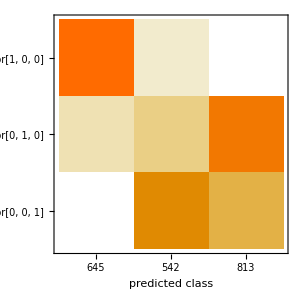

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
result=NetTrain[net,training,
ValidationSet->validation,
TargetDevice->"GPU",
MaxTrainingRounds->10000]
```

NetChain[]

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.997

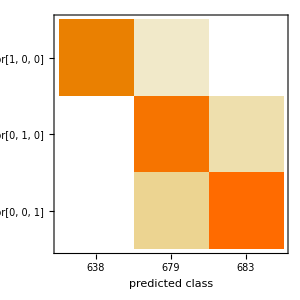

```mathematica
cm["ConfusionMatrixPlot"]
```